```mathematica
ClearAll[a,b,x,t,L,Gtailor,G,y,u,uI,t1,t2,x1,x2,T,TI,X,XI,Gx]
G=(t/Sqrt[4Pi*t]*Exp[-x^2/(4t)])
(*Ginter=Interpolation[Flatten[Table[{x,t,G},{x,1,50},{t,1,50}],1]]*)
data=Flatten[Table[{{x,t},G},{x,0.2,2.5,0.1},{t,0.2,2.5,0.1}],1]//N
pol=InterpolatingPolynomial[data,{x,t}]
```

(ⅇ^(-x^2/(4 t)) √t)/(2 √π)

{{{0.2,0.2},0.120004},{{0.2,0.3},0.149444},{{0.2,0.4},0.174007},{{0.2,0.5},0.195521},{{0.2,0.6},0.214898},{{0.2,0.7},0.23267},{{0.2,0.8},0.249179},{{0.2,0.9},0.264662},{{0.2,1.},0.279288},{{0.2,1.1},0.293186},{{0.2,1.2},0.306455},{{0.2,1.3},0.319173},{{0.2,1.4},0.331403},{{0.2,1.5},0.343199},{{0.2,1.6},0.354602},{{0.2,1.7},0.365649},{{0.2,1.8},0.376373},{{0.2,1.9},0.3868},{{0.2,2.},0.396953},{{0.2,2.1},0.406852},{{0.2,2.2},0.416517},{{0.2,2.3},0.425962},{{0.2,2.4},0.435202},{{0.2,2.5},0.44425},{{0.3,0.2},0.112733},{{0.3,0.3},0.143345},{{0.3,0.4},0.168654},{{0.3,0.5},0.190694},{{0.3,0.6},0.210467},{{0.3,0.7},0.228552},{{0.3,0.8},0.245316},{{0.3,0.9},0.261011},{{0.3,1.},0.275819},{{0.3,1.1},0.289873},{{0.3,1.2},0.303279},{{0.3,1.3},0.316119},{{0.3,1.4},0.328458},{{0.3,1.5},0.34035},{{0.3,1.6},0.351842},{{0.3,1.7},0.362971},{{0.3,1.8},0.373768},{{0.3,1.9},0.384263},{{0.3,2.},0.394479},{{0.3,2.1},0.404438},{{0.3,2.2},0.414157},{{0.3,2.3},0.423653},{{0.3,2.4},0.432941},{{0.3,2.5},0.442035},{{0.4,0.2},0.103288},{{0.4,0.3},0.135223},{{0.4,0.4},0.161434},{{0.4,0.5},0.184135},{{0.4,0.6},0.204417},{{0.4,0.7},0.222909},{{0.4,0.8},0.240008},{{0.4,0.9},0.255985},{{0.4,1.},0.271034},{{0.4,1.1},0.285298},{{0.4,1.2},0.298889},{{0.4,1.3},0.311892},{{0.4,1.4},0.324377},{{0.4,1.5},0.336403},{{0.4,1.6},0.348015},{{0.4,1.7},0.359253},{{0.4,1.8},0.370152},{{0.4,1.9},0.38074},{{0.4,2.},0.391043},{{0.4,2.1},0.401081},{{0.4,2.2},0.410875},{{0.4,2.3},0.420442},{{0.4,2.4},0.429796},{{0.4,2.5},0.438951},{{0.5,0.2},0.0922982},{{0.5,0.3},0.125452},{{0.5,0.4},0.152604},{{0.5,0.5},0.176033},{{0.5,0.6},0.196894},{{0.5,0.7},0.215858},{{0.5,0.8},0.233352},{{0.5,0.9},0.249665},{{0.5,1.},0.265004},{{0.5,1.1},0.279522},{{0.5,1.2},0.293337},{{0.5,1.3},0.30654},{{0.5,1.4},0.319206},{{0.5,1.5},0.331394},{{0.5,1.6},0.343155},{{0.5,1.7},0.35453},{{0.5,1.8},0.365554},{{0.5,1.9},0.376258},{{0.5,2.},0.386668},{{0.5,2.1},0.396807},{{0.5,2.2},0.406695},{{0.5,2.3},0.416349},{{0.5,2.4},0.425786},{{0.5,2.5},0.435018},{{0.6,0.2},0.080441},{{0.6,0.3},0.114464},{{0.6,0.4},0.142465},{{0.6,0.5},0.166612},{{0.6,0.6},0.188073},{{0.6,0.7},0.207542},{{0.6,0.8},0.225466},{{0.6,0.9},0.242151},{{0.6,1.},0.257815},{{0.6,1.1},0.27262},{{0.6,1.2},0.286691},{{0.6,1.3},0.300124},{{0.6,1.4},0.312997},{{0.6,1.5},0.325374},{{0.6,1.6},0.337307},{{0.6,1.7},0.348841},{{0.6,1.8},0.360012},{{0.6,1.9},0.370851},{{0.6,2.},0.381388},{{0.6,2.1},0.391645},{{0.6,2.2},0.401643},{{0.6,2.3},0.411401},{{0.6,2.4},0.420935},{{0.6,2.5},0.43026},{{0.7,0.2},0.0683762},{{0.7,0.3},0.102711},{{0.7,0.4},0.131348},{{0.7,0.5},0.156127},{{0.7,0.6},0.178157},{{0.7,0.7},0.198126},{{0.7,0.8},0.21649},{{0.7,0.9},0.233563},{{0.7,1.},0.249571},{{0.7,1.1},0.264683},{{0.7,1.2},0.27903},{{0.7,1.3},0.292714},{{0.7,1.4},0.305815},{{0.7,1.5},0.3184},{{0.7,1.6},0.330525},{{0.7,1.7},0.342235},{{0.7,1.8},0.35357},{{0.7,1.9},0.364562},{{0.7,2.},0.37524},{{0.7,2.1},0.38563},{{0.7,2.2},0.395753},{{0.7,2.3},0.405628},{{0.7,2.4},0.415273},{{0.7,2.5},0.424702},{{0.8,0.2},0.0566858},{{0.8,0.3},0.0906425},{{0.8,0.4},0.119593},{{0.8,0.5},0.144846},{{0.8,0.6},0.167363},{{0.8,0.7},0.187792},{{0.8,0.8},0.206577},{{0.8,0.9},0.224031},{{0.8,1.},0.240385},{{0.8,1.1},0.255812},{{0.8,1.2},0.270446},{{0.8,1.3},0.284391},{{0.8,1.4},0.297732},{{0.8,1.5},0.310539},{{0.8,1.6},0.322868},{{0.8,1.7},0.334769},{{0.8,1.8},0.34628},{{0.8,1.9},0.357437},{{0.8,2.},0.36827},{{0.8,2.1},0.378805},{{0.8,2.2},0.389064},{{0.8,2.3},0.399068},{{0.8,2.4},0.408835},{{0.8,2.5},0.418379},{{0.9,0.2},0.0458339},{{0.9,0.3},0.0786696},{{0.9,0.4},0.107538},{{0.9,0.5},0.133043},{{0.9,0.6},0.155918},{{0.9,0.7},0.176729},{{0.9,0.8},0.195889},{{0.9,0.9},0.213698},{{0.9,1.},0.230383},{{0.9,1.1},0.246117},{{0.9,1.2},0.261035},{{0.9,1.3},0.275243},{{0.9,1.4},0.288829},{{0.9,1.5},0.301864},{{0.9,1.6},0.314405},{{0.9,1.7},0.326503},{{0.9,1.8},0.3382},{{0.9,1.9},0.349531},{{0.9,2.},0.360527},{{0.9,2.1},0.371216},{{0.9,2.2},0.38162},{{0.9,2.3},0.391762},{{0.9,2.4},0.401659},{{0.9,2.5},0.411327},{{1.,0.2},0.0361445},{{1.,0.3},0.0671496},{{1.,0.4},0.0954973},{{1.,0.5},0.120985},{{1.,0.6},0.14405},{{1.,0.7},0.165135},{{1.,0.8},0.184596},{{1.,0.9},0.202712},{{1.,1.},0.219696},{{1.,1.1},0.235715},{{1.,1.2},0.250904},{{1.,1.3},0.265368},{{1.,1.4},0.279194},{{1.,1.5},0.292454},{{1.,1.6},0.305208},{{1.,1.7},0.317507},{{1.,1.8},0.329392},{{1.,1.9},0.340901},{{1.,2.},0.352065},{{1.,2.1},0.362913},{{1.,2.2},0.373469},{{1.,2.3},0.383754},{{1.,2.4},0.393787},{{1.,2.5},0.403586},{{1.1,0.2},0.0277997},{{1.1,0.3},0.0563692},{{1.1,0.4},0.083751},{{1.1,0.5},0.108926},{{1.1,0.6},0.131982},{{1.1,0.7},0.153203},{{1.1,0.8},0.172871},{{1.1,0.9},0.191225},{{1.1,1.},0.208459},{{1.1,1.1},0.22473},{{1.1,1.2},0.240164},{{1.1,1.3},0.254865},{{1.1,1.4},0.268918},{{1.1,1.5},0.282396},{{1.1,1.6},0.295356},{{1.1,1.7},0.307851},{{1.1,1.8},0.319923},{{1.1,1.9},0.33161},{{1.1,2.},0.342944},{{1.1,2.1},0.353953},{{1.1,2.2},0.364662},{{1.1,2.3},0.375094},{{1.1,2.4},0.385267},{{1.1,2.5},0.395199},{{1.2,0.2},0.0208536},{{1.2,0.3},0.0465374},{{1.2,0.4},0.0725371},{{1.2,0.5},0.097093},{{1.2,0.6},0.119921},{{1.2,0.7},0.141121},{{1.2,0.8},0.160882},{{1.2,0.9},0.17939},{{1.2,1.},0.196811},{{1.2,1.1},0.213284},{{1.2,1.2},0.228927},{{1.2,1.3},0.243838},{{1.2,1.4},0.258097},{{1.2,1.5},0.271775},{{1.2,1.6},0.28493},{{1.2,1.7},0.297613},{{1.2,1.8},0.309865},{{1.2,1.9},0.321725},{{1.2,2.},0.333225},{{1.2,2.1},0.344393},{{1.2,2.2},0.355255},{{1.2,2.3},0.365833},{{1.2,2.4},0.376146},{{1.2,2.5},0.386213},{{1.3,0.2},0.0152568},{{1.3,0.3},0.0377854},{{1.3,0.4},0.0620442},{{1.3,0.5},0.0856843},{{1.3,0.6},0.108058},{{1.3,0.7},0.129067},{{1.3,0.8},0.148792},{{1.3,0.9},0.167355},{{1.3,1.},0.184887},{{1.3,1.1},0.201504},{{1.3,1.2},0.217309},{{1.3,1.3},0.232392},{{1.3,1.4},0.246828},{{1.3,1.5},0.260684},{{1.3,1.6},0.274015},{{1.3,1.7},0.28687},{{1.3,1.8},0.29929},{{1.3,1.9},0.311314},{{1.3,2.},0.322972},{{1.3,2.1},0.334294},{{1.3,2.2},0.345304},{{1.3,2.3},0.356025},{{1.3,2.4},0.366477},{{1.3,2.5},0.376677},{{1.4,0.2},0.0108865},{{1.4,0.3},0.0301723},{{1.4,0.4},0.05241},{{1.4,0.5},0.0748637},{{1.4,0.6},0.0965599},{{1.4,0.7},0.117203},{{1.4,0.8},0.136752},{{1.4,0.9},0.155263},{{1.4,1.},0.172819},{{1.4,1.1},0.18951},{{1.4,1.2},0.205423},{{1.4,1.3},0.220633},{{1.4,1.4},0.23521},{{1.4,1.5},0.249213},{{1.4,1.6},0.262695},{{1.4,1.7},0.275702},{{1.4,1.8},0.288275},{{1.4,1.9},0.300448},{{1.4,2.},0.312254},{{1.4,2.1},0.32372},{{1.4,2.2},0.334871},{{1.4,2.3},0.345729},{{1.4,2.4},0.356313},{{1.4,2.5},0.366643},{{1.5,0.2},0.00757629},{{1.5,0.3},0.0236948},{{1.5,0.4},0.0437218},{{1.5,0.5},0.0647588},{{1.5,0.6},0.0855696},{{1.5,0.7},0.105671},{{1.5,0.8},0.124904},{{1.5,0.9},0.143246},{{1.5,1.},0.160733},{{1.5,1.1},0.177423},{{1.5,1.2},0.193379},{{1.5,1.3},0.208666},{{1.5,1.4},0.22334},{{1.5,1.5},0.237454},{{1.5,1.6},0.251058},{{1.5,1.7},0.264192},{{1.5,1.8},0.276894},{{1.5,1.9},0.2892},{{1.5,2.},0.301137},{{1.5,2.1},0.312735},{{1.5,2.2},0.324015},{{1.5,2.3},0.335001},{{1.5,2.4},0.345711},{{1.5,2.5},0.356163},{{1.6,0.2},0.00514242},{{1.6,0.3},0.0183004},{{1.6,0.4},0.0360208},{{1.6,0.5},0.0554604},{{1.6,0.6},0.0752009},{{1.6,0.7},0.0945965},{{1.6,0.8},0.113372},{{1.6,0.9},0.131427},{{1.6,1.},0.148746},{{1.6,1.1},0.165353},{{1.6,1.2},0.181285},{{1.6,1.3},0.196589},{{1.6,1.4},0.211312},{{1.6,1.5},0.225497},{{1.6,1.6},0.239187},{{1.6,1.7},0.252418},{{1.6,1.8},0.265226},{{1.6,1.9},0.277641},{{1.6,2.},0.289692},{{1.6,2.1},0.301404},{{1.6,2.2},0.3128},{{1.6,2.3},0.323901},{{1.6,2.4},0.334726},{{1.6,2.5},0.345291},{{1.7,0.2},0.00340425},{{1.7,0.3},0.0139005},{{1.7,0.4},0.0293076},{{1.7,0.5},0.0470245},{{1.7,0.6},0.0655402},{{1.7,0.7},0.0840795},{{1.7,0.8},0.102263},{{1.7,0.9},0.119915},{{1.7,1.},0.136967},{{1.7,1.1},0.153405},{{1.7,1.2},0.16924},{{1.7,1.3},0.184501},{{1.7,1.4},0.19922},{{1.7,1.5},0.21343},{{1.7,1.6},0.227166},{{1.7,1.7},0.240461},{{1.7,1.8},0.253344},{{1.7,1.9},0.265843},{{1.7,2.},0.277985},{{1.7,2.1},0.289792},{{1.7,2.2},0.301287},{{1.7,2.3},0.312488},{{1.7,2.4},0.323415},{{1.7,2.5},0.334083},{{1.8,0.2},0.00219795},{{1.8,0.3},0.0103839},{{1.8,0.4},0.0235493},{{1.8,0.5},0.0394751},{{1.8,0.6},0.0566465},{{1.8,0.7},0.0741999},{{1.8,0.8},0.0916678},{{1.8,0.9},0.108806},{{1.8,1.},0.125492},{{1.8,1.1},0.141675},{{1.8,1.2},0.157339},{{1.8,1.3},0.172492},{{1.8,1.4},0.18715},{{1.8,1.5},0.201336},{{1.8,1.6},0.215077},{{1.8,1.7},0.228397},{{1.8,1.8},0.241323},{{1.8,1.9},0.253878},{{1.8,2.},0.266085},{{1.8,2.1},0.277966},{{1.8,2.2},0.289539},{{1.8,2.3},0.300824},{{1.8,2.4},0.311836},{{1.8,2.5},0.322592},{{1.9,0.2},0.00138406},{{1.9,0.3},0.00762875},{{1.9,0.4},0.0186874},{{1.9,0.5},0.0328079},{{1.9,0.6},0.0485534},{{1.9,0.7},0.0650151},{{1.9,0.8},0.0816585},{{1.9,0.9},0.0981783},{{1.9,1.},0.114405},{{1.9,1.1},0.130248},{{1.9,1.2},0.145667},{{1.9,1.3},0.160645},{{1.9,1.4},0.175184},{{1.9,1.5},0.189295},{{1.9,1.6},0.202995},{{1.9,1.7},0.216302},{{1.9,1.8},0.229235},{{1.9,1.9},0.241814},{{1.9,2.},0.254059},{{1.9,2.1},0.265988},{{1.9,2.2},0.277618},{{1.9,2.3},0.288965},{{1.9,2.4},0.300046},{{1.9,2.5},0.310874},{{2.,0.2},0.000850037},{{2.,0.3},0.00551198},{{2.,0.4},0.014645},{{2.,0.5},0.0269955},{{2.,0.6},0.0412711},{{2.,0.7},0.0565618},{{2.,0.8},0.072289},{{2.,0.9},0.0880982},{{2.,1.},0.103777},{{2.,1.1},0.119201},{{2.,1.2},0.134299},{{2.,1.3},0.149037},{{2.,1.4},0.163399},{{2.,1.5},0.177383},{{2.,1.6},0.190995},{{2.,1.7},0.204245},{{2.,1.8},0.217148},{{2.,1.9},0.229718},{{2.,2.},0.241971},{{2.,2.1},0.253921},{{2.,2.2},0.265583},{{2.,2.3},0.276972},{{2.,2.4},0.288101},{{2.,2.5},0.298984},{{2.1,0.2},0.000509169},{{2.1,0.3},0.00391673},{{2.1,0.4},0.0113345},{{2.1,0.5},0.0219918},{{2.1,0.6},0.03479},{{2.1,0.7},0.0488574},{{2.1,0.8},0.0635957},{{2.1,0.9},0.078615},{{2.1,1.},0.0936667},{{2.1,1.1},0.108595},{{2.1,1.2},0.123304},{{2.1,1.3},0.137737},{{2.1,1.4},0.151863},{{2.1,1.5},0.165666},{{2.1,1.6},0.179143},{{2.1,1.7},0.192294},{{2.1,1.8},0.205128},{{2.1,1.9},0.217654},{{2.1,2.},0.229882},{{2.1,2.1},0.241824},{{2.1,2.2},0.253493},{{2.1,2.3},0.264899},{{2.1,2.4},0.276056},{{2.1,2.5},0.286973},{{2.2,0.2},0.00029746},{{2.2,0.3},0.00273717},{{2.2,0.4},0.00866332},{{2.2,0.5},0.0177373},{{2.2,0.6},0.0290833},{{2.2,0.7},0.041902},{{2.2,0.8},0.0555993},{{2.2,0.9},0.069764},{{2.2,1.},0.0841199},{{2.2,1.1},0.0984844},{{2.2,1.2},0.112738},{{2.2,1.3},0.126806},{{2.2,1.4},0.140639},{{2.2,1.5},0.154209},{{2.2,1.6},0.167502},{{2.2,1.7},0.180511},{{2.2,1.8},0.193236},{{2.2,1.9},0.205681},{{2.2,2.},0.217852},{{2.2,2.1},0.229757},{{2.2,2.2},0.241404},{{2.2,2.3},0.252803},{{2.2,2.4},0.263964},{{2.2,2.5},0.274895},{{2.3,0.2},0.000169488},{{2.3,0.3},0.00188123},{{2.3,0.4},0.00653942},{{2.3,0.5},0.0141635},{{2.3,0.6},0.0241109},{{2.3,0.7},0.0356811},{{2.3,0.8},0.0483055},{{2.3,0.9},0.0615665},{{2.3,1.},0.0751693},{{2.3,1.1},0.0889101},{{2.3,1.2},0.10265},{{2.3,1.3},0.116294},{{2.3,1.4},0.129779},{{2.3,1.5},0.143066},{{2.3,1.6},0.156129},{{2.3,1.7},0.168952},{{2.3,1.8},0.181529},{{2.3,1.9},0.193856},{{2.3,2.},0.205936},{{2.3,2.1},0.217772},{{2.3,2.2},0.22937},{{2.3,2.3},0.240735},{{2.3,2.4},0.251876},{{2.3,2.5},0.262799},{{2.4,0.2},0.0000941867},{{2.4,0.3},0.00127158},{{2.4,0.4},0.00487489},{{2.4,0.5},0.0111973},{{2.4,0.6},0.0198228},{{2.4,0.7},0.0301674},{{2.4,0.8},0.0417071},{{2.4,0.9},0.0540313},{{2.4,1.},0.0668361},{{2.4,1.1},0.0799025},{{2.4,1.2},0.0930748},{{2.4,1.3},0.106243},{{2.4,1.4},0.119332},{{2.4,1.5},0.132287},{{2.4,1.6},0.145074},{{2.4,1.7},0.157669},{{2.4,1.8},0.170057},{{2.4,1.9},0.182231},{{2.4,2.},0.194186},{{2.4,2.1},0.205922},{{2.4,2.2},0.217441},{{2.4,2.3},0.228746},{{2.4,2.4},0.239841},{{2.4,2.5},0.250733},{{2.5,0.2},0.0000510487},{{2.5,0.3},0.000845289},{{2.5,0.4},0.00358891},{{2.5,0.5},0.00876415},{{2.5,0.6},0.016162},{{2.5,0.7},0.0253243},{{2.5,0.8},0.0357856},{{2.5,0.9},0.0471556},{{2.5,1.},0.0591303},{{2.5,1.1},0.0714819},{{2.5,1.2},0.0840423},{{2.5,1.3},0.0966892},{{2.5,1.4},0.109334},{{2.5,1.5},0.121913},{{2.5,1.6},0.134381},{{2.5,1.7},0.146707},{{2.5,1.8},0.158869},{{2.5,1.9},0.170853},{{2.5,2.},0.182649},{{2.5,2.1},0.194254},{{2.5,2.2},0.205664},{{2.5,2.3},0.216881},{{2.5,2.4},0.227907},{{2.5,2.5},0.238743}}

0.037155+t (0.207214+t (3.37822+t (-30.0799+t (151.68+t (-533.022+t (1397.44+t (-2823.51+t (4461.46+t (-5521.7+t (5288.25+t (-3788.84+t (1857.04+t (-425.52+t (-175.661+t (219.321+t (-103.58+t (26.0744+t (-2.42299+t (-0.406063+t (0.145493+t (-0.0672155+t (0.0427893+t (-0.0138138+t (0.00206204+t (-0.000214364+t (0.0000729343+t (-0.0000139231+t (-1.26228×10^-6+t (6.20066×10^-7+t (-7.28868×10^-8+(1.54703×10^-8-2.29448×10^-9 t) t))))))))))))))))))))))))))))))+x (0.399259+t (1.55967+t (-16.0851+t (99.4536+t (-396.163+t (1125.49+t (-2402.22+t (4008.95+t (-5420.98+t (6114.9+t (-5830.7+t (4650.1+t (-2996.62+t (1473.59+t (-499.979+t (86.8965+t (9.63797+t (-9.1585+t (1.70999+t (0.0873244+t (-0.0999275+t (0.0328951+t (-0.00895399+t (0.000632796+t (0.000377841+t (-0.0000622822+t (-9.47844×10^-6+t (1.90562×10^-6+t (-2.30139×10^-9+t (1.15326×10^-7+(-4.75864×10^-8+5.38157×10^-9 t) t)))))))))))))))))))))))))))))+x (-5.74949+t (1.42044+t (1.57602+t (-82.5726+t (391.748+t (-1131.29+t (2236.+t (-3073.91+t (2829.84+t (-1476.33+t (-6.34723+t (674.286+t (-523.142+t (152.852+t (36.56+t (-51.4798+t (21.7284+t (-5.19331+t (0.851517+t (-0.0945111+t (-0.0141645+t (0.00715637+t (0.00110423+t (-0.000832938+t (0.000114026+t (-0.000015895+t (6.31334×10^-6+t (-1.11045×10^-6+t (1.7603×10^-7+(-3.11237×10^-8+1.26347×10^-9 t) t))))))))))))))))))))))))))))+x (38.173+t (-7.2243+t (59.8804+t (-43.1757+t (42.9942+t (-92.0234+t (132.638+t (-60.7353+t (-41.8803+t (-14.3342+t (225.688+t (-378.306+t (330.517+t (-167.473+t (41.9629+t (1.47002+t (-3.71319+t (0.556078+t (0.136763+t (-0.0361284+t (-0.000410377+t (-0.000685736+t (0.000210649+t (0.000078464+t (-0.0000108951+t (-4.92392×10^-7+t (-6.88568×10^-7+t (6.56242×10^-8+(8.24046×10^-10+3.31825×10^-9 t) t)))))))))))))))))))))))))))+x (-178.919+t (11.3573+t (-205.986+t (-65.6434+t (455.152+t (-552.882+t (-62.656+t (1157.72+t (-1996.13+t (2010.34+t (-1339.63+t (604.769+t (-188.068+t (43.1744+t (-7.87038+t (0.451114+t (0.434552+t (-0.149184+t (0.028573+t (-0.013895+t (0.0042279+t (0.0000843492+t (-0.000111311+t (-0.0000500216+t (0.000012211+t (8.80835×10^-7+t (-3.07468×10^-7+(5.25245×10^-8-9.21073×10^-9 t) t))))))))))))))))))))))))))+x (607.752+t (-8.23539+t (799.154+t (-192.751+t (-854.663+t (1884.5+t (-2192.86+t (1716.9+t (-814.195+t (42.7539+t (210.268+t (-120.077+t (16.6423+t (7.20073+t (-2.35669+t (-0.182936+t (0.128285+t (0.00909144+t (-0.00962757+t (0.00173955+t (-0.000437105+t (0.0000294809+t (0.0000440623+t (-6.96165×10^-6+t (-6.98393×10^-7+t (4.66065×10^-8+(4.45592×10^-8-7.5397×10^-9 t) t)))))))))))))))))))))))))+x (-1532.26+t (-141.372+t (-2048.21+t (1159.78+t (51.269+t (-1037.37+t (1187.99+t (-952.504+t (665.702+t (-306.738+t (64.1928+t (1.69842+t (2.52753+t (-3.96068+t (0.920511+t (0.0408501+t (-0.0282622+t (-0.000105931+t (0.00164753+t (-0.000316587+t (-0.0000232226+t (0.0000188715+t (-3.26885×10^-6+t (-1.22257×10^-6+t (1.04556×10^-7+(1.44604×10^-8+5.7396×10^-9 t) t))))))))))))))))))))))))+x (2930.56+t (713.448+t (3610.36+t (-2142.92+t (592.513+t (462.772+t (-344.99+t (-84.4825+t (128.688+t (-69.436+t (37.0375+t (-19.8546+t (5.27091+t (0.282732+t (-0.301963+t (0.0405142+t (-0.0116114+t (0.00158151+t (0.000302205+t (-0.000114288+t (5.84214×10^-6+t (4.43583×10^-6+t (1.22445×10^-6+t (-1.35909×10^-7+(9.43934×10^-9-6.89064×10^-9 t) t)))))))))))))))))))))))+x (-4284.43+t (-1838.23+t (-4777.32+t (2649.76+t (-825.432+t (-441.715+t (517.849+t (-69.3009+t (-55.4499+t (33.2893+t (-3.05768+t (-0.188644+t (-0.854176+t (0.0925482+t (0.0303304+t (-0.00226617+t (0.00194153+t (0.0000104915+t (-0.0000879651+t (-3.60164×10^-6+t (-2.5052×10^-6+t (3.88873×10^-8+t (-1.28881×10^-7+(-3.05209×10^-8+7.26851×10^-9 t) t))))))))))))))))))))))+x (4736.03+t (3165.32+t (4876.32+t (-2436.52+t (834.037+t (157.733+t (-390.908+t (125.317+t (-17.8008+t (-8.34797+t (0.191863+t (1.65301+t (-0.0232361+t (-0.0579344+t (-0.00175392+t (0.000378329+t (-0.000138917+t (-4.18996×10^-6+t (7.21092×10^-6+t (-2.63312×10^-7+t (1.09968×10^-6+t (1.25117×10^-7+(-4.52196×10^-8+3.18244×10^-9 t) t)))))))))))))))))))))+x (-3778.19+t (-3942.67+t (-3883.08+t (1652.4+t (-518.357+t (64.6463+t (128.085+t (-37.5924+t (13.0667+t (2.20657+t (-1.4003+t (-0.221861+t (-0.0177199+t (0.0247578+t (-0.00144918+t (-0.000438234+t (0.0000779807+t (-9.71646×10^-6+t (-2.24346×10^-6+t (1.02606×10^-6+t (-6.05719×10^-8+(-2.92346×10^-8+2.31065×10^-9 t) t))))))))))))))))))))+x (1829.25+t (3662.57+t (2446.74+t (-854.233+t (139.722+t (-60.5531+t (-20.0393+t (-4.3035+t (-2.26573+t (-0.0185827+t (0.38193+t (0.0203236+t (-0.00225343+t (0.000132088+t (-0.000167899+t (0.0000159049+t (0.0000287393+t (-1.13282×10^-6+t (-2.86117×10^-7+t (-2.22625×10^-7+(9.18689×10^-9+3.47789×10^-9 t) t)))))))))))))))))))+x (37.4355+t (-2563.5+t (-1233.1+t (379.969+t (27.4026+t (9.9131+t (5.13356+t (3.10468+t (0.224284+t (-0.150917+t (-0.0323433+t (-0.002784+t (-0.000186517+t (-0.000546458+t (0.0000966531+t (-1.79618×10^-6+t (-6.14358×10^-6+t (-3.13722×10^-7+t (6.42683×10^-8+(4.43257×10^-8+2.66688×10^-9 t) t))))))))))))))))))+x (-989.87+t (1344.41+t (493.193+t (-164.774+t (-31.1154+t (3.12437+t (-1.17205+t (-0.0128193+t (-0.232924+t (0.0815546+t (-0.00534774+t (0.000164574+t (0.000372498+t (-0.0000769903+t (-2.3624×10^-6+t (2.43489×10^-6+t (9.31822×10^-7+t (1.59197×10^-8+(5.18437×10^-9-6.30943×10^-9 t) t)))))))))))))))))+x (998.013+t (-513.096+t (-149.599+t (63.5419+t (7.58038+t (-1.7219+t (-0.771673+t (0.107152+t (-0.0309614+t (-0.0000979457+t (-0.00024991+t (0.000422388+t (-0.0000989539+t (0.0000245193+t (-9.52388×10^-7+t (-1.73329×10^-7+t (-4.53208×10^-8+(-1.34512×10^-8-7.93891×10^-9 t) t))))))))))))))))+x (-579.701+t (129.409+t (29.9583+t (-16.525+t (0.277526+t (0.651118+t (0.258155+t (-0.0346726+t (0.0285023+t (-0.00312779+t (-0.000563488+t (0.0000493222+t (0.0000271904+t (-1.47726×10^-6+t (-3.72064×10^-8+t (-1.29778×10^-7+(4.98033×10^-8+8.56256×10^-10 t) t)))))))))))))))+x (209.261+t (-12.094+t (-1.19404+t (1.52518+t (-0.541234+t (-0.10443+t (0.00841447+t (-0.014535+t (0.000248766+t (0.0000736453+t (0.0000706025+t (-0.0000118386+t (-3.00897×10^-6+t (-4.06414×10^-7+t (-1.57114×10^-7+(4.17305×10^-8-5.82063×10^-9 t) t))))))))))))))+x (-36.1633+t (-6.43023+t (-2.11411+t (0.49597+t (0.11514+t (-0.0412487+t (0.00181149+t (0.000486457+t (-0.000361556+t (-0.0000789685+t (0.0000415341+t (7.57466×10^-8+t (-4.09893×10^-7+t (-1.19182×10^-7+(-6.69188×10^-9+3.74161×10^-9 t) t)))))))))))))+x (-5.31232+t (3.71451+t (1.16334+t (-0.189393+t (-0.00632328+t (0.0114922+t (-0.00144485+t (0.000267625+t (-0.0000151962+t (4.92423×10^-6+t (-2.10131×10^-6+t (-4.3549×10^-7+t (-2.33825×10^-7+(5.9562×10^-8+1.30201×10^-8 t) t))))))))))))+x (4.559+t (-0.812361+t (-0.358006+t (0.0384588+t (-0.00145806+t (0.00112549+t (-0.000162446+t (0.000143804+t (-0.0000108799+t (-1.45234×10^-6+t (1.60334×10^-7+t (3.18141×10^-7+t (2.21223×10^-8+(1.37088×10^-9-1.95457×10^-10 t) t))))))))))))+x (-0.850034+t (-0.0613239+t (0.0663502+t (-0.0115397+t (0.00155748+t (-0.000509693+t (3.45812×10^-6+t (4.12516×10^-6+t (3.18011×10^-6+t (-2.21397×10^-7+t (-2.83376×10^-7+t (-3.37064×10^-8+(-7.55598×10^-9-2.90604×10^-9 t) t)))))))))))+x (-0.0682228+t (0.0775652+t (-0.00987611+t (0.00294228+t (-0.000658612+t (0.000119156+t (-0.0000174343+t (-8.08973×10^-7+t (1.17887×10^-6+t (6.12562×10^-8+t (2.64144×10^-8+(1.17251×10^-8-1.04287×10^-9 t) t))))))))))+x (0.0557687+t (-0.00909657+t (0.00244127+t (-0.000192312+t (-0.0000198096+t (-0.000033758+t (3.43506×10^-6+t (-2.16098×10^-6+t (-3.60563×10^-7+t (-7.40785×10^-8+(3.85623×10^-8-4.96157×10^-10 t) t)))))))))+x (-0.0130323+t (-0.00332026+t (-0.000231239+t (-0.0000927354+t (0.0000658288+t (1.10497×10^-6+t (5.66221×10^-7+t (-9.96756×10^-8+t (6.83339×10^-8+(-8.13625×10^-9-2.70382×10^-9 t) t))))))))+x (0.00407248+t (0.000594993+t (-0.000165229+t (0.0000256942+t (-9.50881×10^-6+t (8.26374×10^-7+t (4.39043×10^-7+t (5.22595×10^-8+(-1.24976×10^-9-2.66473×10^-9 t) t)))))))+x (-0.00107482+t (0.0000566797+t (0.0000611423+t (-4.19689×10^-6+t (-9.34932×10^-7+t (6.30859×10^-10+t (-5.35682×10^-8+(-7.21181×10^-9+2.73525×10^-9 t) t))))))+x (0.0000260675+t (0.000029454+t (-0.0000116255+t (1.71309×10^-6+t (1.7605×10^-7+t (-1.61812×10^-8+(-7.37021×10^-9+3.9475×10^-9 t) t)))))+x (0.0000479083+t (-0.0000121022+t (1.80445×10^-6+t (-5.29771×10^-7+t (6.88171×10^-9+(-4.58305×10^-9-4.66651×10^-9 t) t))))+x (-7.05111×10^-6+t (-5.6227×10^-7+t (-6.95896×10^-8+t (5.19241×10^-8+(-1.63751×10^-8+2.71135×10^-9 t) t)))+x (-1.3349×10^-7+t (5.82954×10^-8+t (-4.95922×10^-8+(1.38745×10^-8+4.46141×10^-9 t) t))+x (-2.53014×10^-8+t (1.0014×10^-7+(1.31179×10^-8-3.78888×10^-9 t) t)+x (2.10461×10^-8+(-3.35908×10^-9-1.29415×10^-9 t) t+(3.31308×10^-10-1.75104×10^-9 t-3.2824×10^-10 x) x)))))))))))))))))))))))))))))))

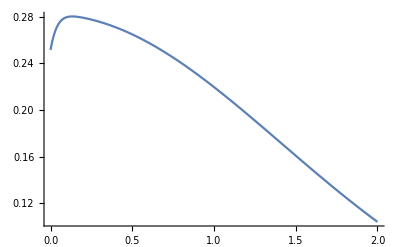

```mathematica
Plot[pol/.{t->1},{x,0,2}]
```

```mathematica
Integrate[G,Evaluate[XI],Evaluate[TI]]
```

(ⅇ^(-x^2/(4 t)) √t TI XI)/(2 √π)

```mathematica
2^6
```

64

```mathematica
(2^3)^2
```

64